Definition of Constants

```mathematica
Subscript[C, A]=0.0096932;
λ=0.5*10^-6;
Subscript[k, 0]=(2*π)/λ;
(*Hufnagel-Valley Constants for Daytime*)
Aturb = 1.7*10^-14;
vturb = 21.0;
Subscript[R, m]=0.5; (*This is the physical aperture size*)
```

Basic Equation Definitions

```mathematica
Subscript[C, n][ht_Real?NumericQ]:= 5.94*10^-53*(vturb/27.0)^2*ht^10*ⅇ^(-ht/1000)+2.7*10^-16*ⅇ^(-ht/1500)+Aturb*ⅇ^(-ht/100) (*Subscript[C, n]^2 Hufnagel-Valley EQN*)
Subscript[R, 1][apht_Real?NumericQ] := Subscript[R, m]; (*For plane wave case R1 is a constant equal to Rm*)
HJ1pre=MellinTransform[BesselJ[0,x],x,s];
HJ1=N[HJ1pre/.s->-5/3];
```

```mathematica
A0Large[β_]:=((1^2*2^(-5/3)*Gamma[14/3]*Gamma[1-11/6])/((Gamma[17/6])^2*Gamma[17/6+1])-(1^2*β^(-2*(1-11/6))*Gamma[1-11/6])/(2^(2*(1-1))*(Gamma[1+1])^2*Gamma[17/6-1]))*(HypergeometricPFQ[{1+1/2,1-11/6,1-11/6},{1+1,2*1+1},1/β^2]);(*β>1*)
```

```mathematica
A1Large[β_]:=((2^2*2^(-5/3)*Gamma[14/3]*Gamma[2-11/6])/((Gamma[17/6])^2*Gamma[17/6+2])-(2^2*β^(-2*(2-11/6))*Gamma[2-11/6])/(2^(2*(2-1))*(Gamma[2+1])^2*Gamma[17/6-2]))*(HypergeometricPFQ[{2+1/2,2-11/6,2-11/6},{2+1,2*2+1},1/β^2]);
```

```mathematica
A0Small[β_]:=-(1^2*2^(-5/3)*Gamma[14/3]*Gamma[1-11/6])/((Gamma[17/6])^2*Gamma[17/6+1])*(HypergeometricPFQ[{1-11/6,-1-11/6,-11/6},{-4/3,1},β^2])-(4*1^2*β^(14/3)*Gamma[-7/3])/(π*Gamma[10/3])*(HypergeometricPFQ[{1+1/2,-1+1/2,1/2},{10/3,10/3},β^2]);
```

```mathematica
A1Small[β_]:=-(2^2*2^(-5/3)*Gamma[14/3]*Gamma[2-11/6])/((Gamma[17/6])^2*Gamma[17/6+2])*(HypergeometricPFQ[{2-11/6,-2-11/6,-11/6},{-4/3,1},β^2])-(4*2^2*β^(14/3)*Gamma[-7/3])/(π*Gamma[10/3])*(HypergeometricPFQ[{2+1/2,-2+1/2,1/2},{10/3,10/3},β^2]);
```

```mathematica
A0[β_]:=Piecewise[{{A0Small[β],β<1},{A0Large[β],β>1}}]
```

```mathematica
A1[β_]:=Piecewise[{{A1Small[β],β<1},{A1Large[β],β>1}}]
```

```mathematica
Y[S_]:=(((S*Abs[θ])/(Subscript[R, 1][S]))^(5/3)*Abs[HJ1])-A0[(S*Abs[θ])/(2*Subscript[R, 1][S])]-A1[(S*Abs[θ])/(2*Subscript[R, 1][S])](*Piston and Tilt removed*)(*Issue is in the Subscript[A, 0] and Subscript[A, 1] terms(as seen in the plots below*)
```

```mathematica
YNP[S_]:=(((S*Abs[θ])/(Subscript[R, 1][S]))^(5/3)*Abs[HJ1])-A0[(S*Abs[θ])/(2*Subscript[R, 1][S])]
(*Piston removed*)
```

```mathematica
Ytot[S_]:=((S*Abs[θ])/(Subscript[R, 1][S]))^(5/3)*Abs[HJ1](*this one works just fine*)
(*Nothing removed*)
```

```mathematica
Anisodeg[θ_]=2*(2*π)^(8/3)*Subscript[C, A]*Subscript[k, 0]^2*NIntegrate[Subscript[C, n][S]*(Subscript[R, 1][S])^(5/3)*Y[S],{S,0,∞}];
(*Piston and Tilt removed*)
```

NIntegrate::inumr: The integrand C_n[S] (-(Piecewise[{{Times[«7»]+Times[«8»], Times[«4»]<1}, {HypergeometricPFQ[«3»] Plus[«2»], Times[«4»]>1}, {0, True}}])-(Piecewise[{{Times[«7»]+Times[«8»], Times[«4»]<1}, {HypergeometricPFQ[«3»] Plus[«2»], Times[«4»]>1}, {0, True}}])+1.11833 Abs[θ]^(5/3) (S/R_1[S])^(5/3)) R_1[S]^(5/3) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
AnisodegNoPiston[θ_]=2*(2*π)^(8/3)*Subscript[C, A]*Subscript[k, 0]^2*NIntegrate[Subscript[C, n][S]*(Subscript[R, 1][S])^(5/3)*YNP[S],{S,0,∞}];
(*Piston removed*)
```

NIntegrate::inumr: The integrand C_n[S] (-(Piecewise[{{Times[«7»]+Times[«8»], Times[«4»]<1}, {HypergeometricPFQ[«3»] Plus[«2»], Times[«4»]>1}, {0, True}}])+1.11833 Abs[θ]^(5/3) (S/R_1[S])^(5/3)) R_1[S]^(5/3) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
Anisodegtot[θ_]=2*(2*π)^(8/3)*Subscript[C, A]*Subscript[k, 0]^2*NIntegrate[Subscript[C, n][S]*(Subscript[R, 1][S])^(5/3)*Ytot[S],{S,0,∞}];
(*Nothing removed*)
```

NIntegrate::inumr: The integrand 1.11833 Abs[θ]^(5/3) C_n[S] (S/R_1[S])^(5/3) R_1[S]^(5/3) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in S near {S} = {17685.4}. NIntegrate obtained 2.18928×10^-22 and 1.44478×10^-26 for the integral and error estimates.

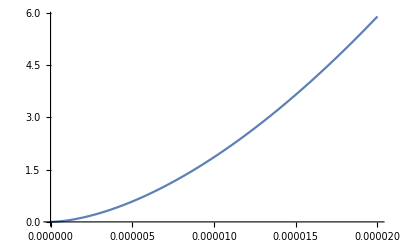

```mathematica
Plot[Abs[Anisodegtot[θ]],{θ,0,2.0*10^-5}] (*Nothing removed*)(*Abs[] not necessary for this, just there for consistency*)
```

```mathematica
(*Without abs[] both of these are inverted over the x axis IE 82.5 -> -82.5*)
```

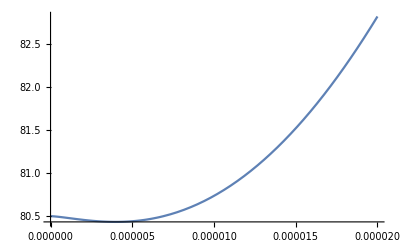

```mathematica
Plot[Abs[Anisodeg[θ]],{θ,0,2.0*10^-5}](*Piston and Tilt removed*)
```

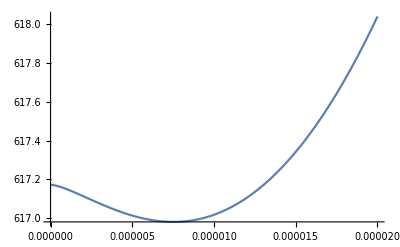

```mathematica
Plot[Abs[AnisodegNoPiston[θ]],{θ,0,2.0*10^-5}]
(*Piston removed*)
```